http://www.staff.science.uu.nl/~gent0113/babylon/babycal.htm

http://www.staff.science.uu.nl/~gent0113/babylon/downloads/babylonian_chronology_pd_1971.dat

```mathematica
rawText=URLRead["http://www.staff.science.uu.nl/~gent0113/babylon/downloads/babylonian_chronology_pd_1971.dat","Body"];
```

```mathematica
rawTable=Map[ToExpression,StringSplit[StringSplit[rawText,"\r\n"],Whitespace][[All,;;5]],{2}];
```

```mathematica
adjustedTable=MapAt[If[#<1,#-1,#]&,rawTable,{All,3}];
```

```mathematica
adjustedTable
```

{{-314,1,-626,4,5},{-314,2,-626,5,5},{-314,3,-626,6,4},{-314,4,-626,7,3},{-314,5,-626,8,2},{-314,6,-626,8,31},{-314,7,-626,9,29},{-314,8,-626,10,29},{-314,9,-626,11,27},8653,{386,5,75,8,3},{386,6,75,9,2},{386,7,75,10,1},{386,8,75,10,31},{386,9,75,11,29},{386,10,75,12,28},{386,11,76,1,26},{386,12,76,2,25}}
 |  |  |  |

```mathematica
monthMap=Association[Rule@@TakeDrop[#,2]&/@adjustedTable];
```

```mathematica
fromBabylonianDate[{y_,m_,d_}]:=Catch[DateObject[Lookup[monthMap,Key[{y,m}],Throw[Missing[]]]+{0,0,d-1},CalendarType->"Julian"]]
```

```mathematica
fromBabylonianDate[{148,2,4}]
```

Day: Wed 29 Apr -164 (Juliancalendar)

```mathematica
Round@DateValue[fromBabylonianDate[{148,2,4}],"JulianDate"]
```

1661641

```mathematica
SelectFirst[]
```

```mathematica
toBabylonianDate[date_]:=Lookup[inverseMonthMap,Key[DateValue[date,{"Year","Month","Day"}]]]
```

```mathematica
inverseMonthMap
```

<|{-626,4,5}→{-314,1},{-626,5,5}→{-314,2},{-626,6,4}→{-314,3},{-626,7,3}→{-314,4},{-626,8,2}→{-314,5},{-626,8,31}→{-314,6},{-626,9,29}→{-314,7},8656,{75,9,2}→{386,6},{75,10,1}→{386,7},{75,10,31}→{386,8},{75,11,29}→{386,9},{75,12,28}→{386,10},{76,1,26}→{386,11},{76,2,25}→{386,12}|>
 |  |  |  |

```mathematica
CalendarConvert[1661641,"JulainDate"]
```

CalendarConvert::nodobj: First argument 1661641 in CalendarConvert is not a DateObject.

CalendarConvert[1661641,JulainDate]

```mathematica
ArrayPlot@Transpose@Partition[Values@Boole[Length[#]===13&/@GroupBy[rawTable,First->(#[[2]]&)]],19]
```

-Graphics-

```mathematica
Total/@Partition[Values@Boole[Length[#]===13&/@GroupBy[adjustedTable,First->(#[[2]]&)]],19]
```

{6,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7}

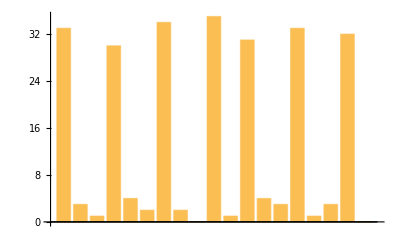

```mathematica
BarChart@Total@Partition[Values@Boole[Length[#]===13&/@GroupBy[adjustedTable,First->(#[[2]]&)]],19]
```

```mathematica
ArrayPlot@Transpose@Partition[Values@Boole[Length[#]===13&/@GroupBy[rawTable,First->(#[[2]]&)]],19]
```

-Graphics-

```mathematica
ArrayPlot@Transpose@Partition[Values[Switch[Complement[#,Range[12]],{},0,{6b},1,{12b},2]&/@GroupBy[rawTable,First->(#[[2]]&)]],19]
```

-Graphics-